```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

E:\LPAchebshevdeta\buffer

```mathematica
list=Flatten[Import["b.dat"]];
```

```mathematica
list2=Rest[list];
```

```mathematica
10^-2.655
```

0.00221309

```mathematica
10^-1.278
```

0.052723

```mathematica
ρmin=0;
ρmax=9000;
c0=1.85*10^6;
fpi=93.5;
```

```mathematica
eqn7=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-Exp[c]*(2ρ)^(-1/2),40])]==0,{c,Log[0.05],Log[0.4],(Log[0.4]-Log[0.05])/19}];
```

```mathematica
res7=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->38]&,eqn7]][[All,2]]
```

{0.54811021330653173444507316842376686413,0.58177322166957266243276596221426911537,0.61811318757073583581888917312086483918,0.65734276745217203392985328557175012033,0.69969269238801209225312426008700980048,0.74541341597513337112242129921339049297,0.7947769211340938169735588097673058245,0.8480787014134580079233297739602448923,0.90563993337700306773693809975216200825,0.96780985745701003391393678615189480767,1.0349683851551944235438481084301212196,1.1075289504956310604998050535019328375,1.1859416229491747356152249614971949938,1.2706964973444079688265647957141792564,1.3623273731426162413234682830370011408,1.4614157303440022403829890104906117306,1.5685950015166213387552971839503359067,1.6845551281271240081753382371618714194,1.8100473734349281809638734735389363186,1.9458893424223261077204960424846230779}

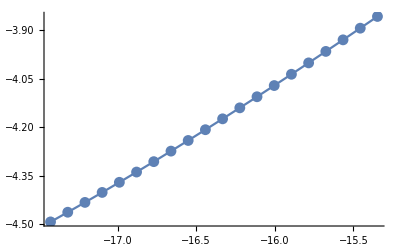

```mathematica
ListLinePlot[data7=Transpose[{Table[Log[Exp[c]/c0],{c,Log[0.05],Log[0.4],(Log[0.4]-Log[0.05])/19}],Log[Sqrt[res7*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data7,{1,x},x]
```

0.817335+0.305284 x

```mathematica
fit7=LinearModelFit[data7,x,x]
```

FittedModel[0.817335+0.305284 x]

```mathematica
fit7[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.817335 | 0.0316773 | 25.802 | 1.14001×10^-15
x | 0.305284 | 0.00193167 | 158.041 | 9.66495×10^-30, | Estimate | Standard Error | Confidence Interval
1 | 0.817335 | 0.0316773 | {0.750784,0.883887}
x | 0.305284 | 0.00193167 | {0.301225,0.309342}}

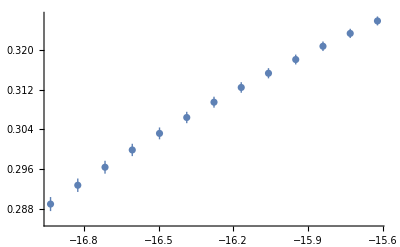

```mathematica
ListPlot[Table[fit7=LinearModelFit[data7[[n;;n+5]],x,x];
{data7[[n;;n+5]][[All,1]]//Mean,Around@@Normal[fit7["ParameterTable"]][[1,3,{2,3}]]},{n,3,Length[data7]-5}]]
```

```mathematica
tempdat1=Table[fit7=LinearModelFit[data7[[n;;n+5]],x,x];
{data7[[n;;n+5]][[All,1]]//Mean,Around@@Normal[fit7["ParameterTable"]][[1,3,{2,3}]]},{n,3,Length[data7]-5}]
```

{{-16.9339,0.28900.0014},{-16.8245,0.29280.0013},{-16.715,0.29640.0013},{-16.6056,0.29990.0012},{-16.4962,0.30320.0012},{-16.3867,0.30640.0011},{-16.2773,0.30950.0011},{-16.1678,0.31240.0011},{-16.0584,0.31530.0010},{-15.9489,0.31800.0010},{-15.8395,0.32070.0010},{-15.73,0.32330.0009},{-15.6206,0.32580.0009}}

```mathematica
Exp[Transpose[tempdat1][[1]]]*c0
```

{0.08182,0.0912832,0.101841,0.11362,0.126761,0.141421,0.157778,0.176026,0.196385,0.219098,0.244439,0.27271,0.304251}

```mathematica
Export["hdata1.dat",c0*Exp[Transpose[tempdat1][[1]]]]
```

hdata1.dat

```mathematica
Export["zdata1.dat",Transpose[tempdat1][[2]]/.Around->List]
```

zdata1.dat

```mathematica
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-Exp[c]*(2ρ)^(-1/2),40])]==0,{c,Log[0.001],Log[10^5],(Log[10^5]-Log[0.001])/50}];
```

```mathematica
res6=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->38]&,eqn6]][[All,2]]
```

{0.1648054132059968962263465540562916115,0.17078386878604713812810586858613867297,0.1791078175764631319372119740144482786,0.19057755968297395445554861191794048249,0.20620381185345309378784510954695964647,0.22724906803892612501019210559856478464,0.2552867461982896530028282702506616684,0.29228878951815809213403199703188682797,0.34075162675735942195254208734636566816,0.40386974979435601648840827507920679995,0.48576837365356190661587810150862277324,0.5918127620808807960338656383601168169,0.72902151007357359892776913776312897465,0.90662396242243022221255650153727341706,1.1368176703730159990882301425753138141,1.4357981059374299516032860579920084001,1.8251401969998972542377037176804823133,2.3335800921967911735545195367413386289,2.9991015372816664653589414534239221844,3.8708286699584931644253793043342308407,5.0094230927024945698447456073119962943,6.4838479614005850512709191534611047107,8.3634798860325654477780025910656819932,10.710270916350438847090065842502044544,13.58165643125025235829761323174505263,17.048727490178914785580142075884966693,21.219221093777210271369527486277473134,26.250237489215690215683153208210142432,32.33899808384984531887471706111755451,39.683417559701275950633912496409952551,48.431300463672031221131232308039175387,58.686241248830358241660941348478816906,70.596015618494573621941047296745777525,84.418216125380571753496853634979256033,100.47111139954411882077201045236179476,119.03759087181824685710413383964897039,140.38761656653835015858936335749159462,164.91070126450219999554508688551553403,193.11828381917300501470924518738020194,225.51400579026734211478689031449795286,262.63918051174609931614472140355667802,305.20253695402554193785568742645834085,353.96466291099828714132107060851431536,409.73624321304395402251598284821092053,473.50609547995107059821615579267746943,546.31289519841450977322920426008301618,629.35306141730188381021319870238921463,723.95005592652302820754045848925913565,831.59054826169017241793686657631555741,953.94787394573534772352368547555029411,1092.9426814595830546727070442368231041}

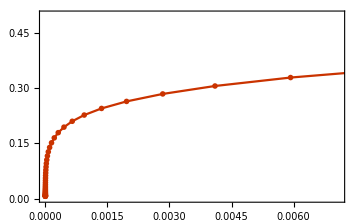

```mathematica
ListLinePlot[data8=Transpose[{Table[Exp[c]/c0,{c,Log[0.001],Log[10^5],(Log[10^5]-Log[0.001])/50}],Sqrt[res6*2]/fpi}]]
```

```mathematica
fit=Fit[data8,{1,x^(1/5),x^(1/3),x},x]
```

-0.0163238+0.911127 x^(1/5)+0.142461 x^(1/3)-0.94367 x

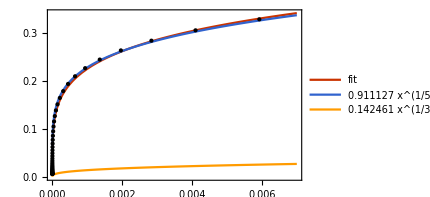

```mathematica
Plot[{fit,0.9111267751083686 x^(1/5),0.14246137759158325 x^(1/3)},{x,-0.000001,0.007},Epilog->Point[data8],PlotLegends->"Expressions"]
```

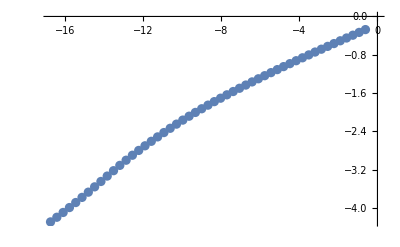

```mathematica
ListLinePlot[data6=Transpose[{Table[Log[Exp[c]/c0],{c,Log[0.1],Log[10^6],(Log[10^6]-Log[0.1])/50}],Log[Sqrt[res6*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data6,{1,x},x]
```

0.117348+0.246957 x

```mathematica
fit6=LinearModelFit[data6,x,x]
```

FittedModel[0.117348+0.246957 x]

```mathematica
fit6[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.118016 | 0.0390082 | 3.02543 | 0.00367444
x | 0.246933 | 0.00394822 | 62.5429 | 1.23493×10^-55, | Estimate | Standard Error | Confidence Interval
1 | 0.118016 | 0.0390082 | {0.0399612,0.196072}
x | 0.246933 | 0.00394822 | {0.239033,0.254834}}

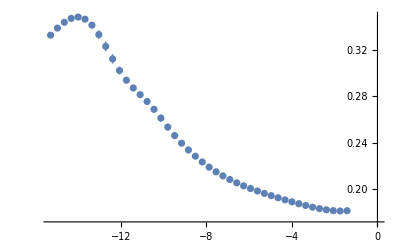

```mathematica
ListPlot[Table[fit6=LinearModelFit[data6[[n;;n+5]],x,x];
{data6[[n;;n+5]][[All,1]]//Mean,Around@@Normal[fit6["ParameterTable"]][[1,3,{2,3}]]},{n,3,Length[data6]-5}]]
```

```mathematica
tempdat=Table[fit6=LinearModelFit[data6[[n;;n+5]],x,x];
{data6[[n;;n+5]][[All,1]]//Mean,Around@@Normal[fit6["ParameterTable"]][[1,3,{2,3}]]},{n,3,Length[data6]-5}]
```

{{-15.2827,0.33250.0024},{-14.9603,0.33860.0021},{-14.6379,0.34360.0017},{-14.3156,0.34700.0010},{-13.9932,0.34810.0005},{-13.6708,0.34630.0014},{-13.3485,0.34110.0026},{-13.0261,0.3330.004},{-12.7038,0.3230.004},{-12.3814,0.3120.004},{-12.059,0.30210.0034},{-11.7367,0.29370.0027},{-11.4143,0.28700.0021},{-11.0919,0.28130.0019},{-10.7696,0.27530.0022},{-10.4472,0.26860.0027},{-10.1249,0.26110.0030},{-9.8025,0.25330.0029},{-9.48014,0.24600.0025},{-9.15778,0.23950.0022},{-8.83541,0.23370.0020},{-8.51305,0.22830.0019},{-8.19069,0.22330.0018},{-7.86833,0.21880.0015},{-7.54597,0.21480.0013},{-7.2236,0.21130.0012},{-6.90124,0.20820.0011},{-6.57888,0.20540.0010},{-6.25652,0.20280.0009},{-5.93416,0.20040.0008},{-5.6118,0.19830.0008},{-5.28943,0.19620.0007},{-4.96707,0.19430.0007},{-4.64471,0.19250.0007},{-4.32235,0.19070.0006},{-3.99999,0.18900.0006},{-3.67762,0.18740.0006},{-3.35526,0.18580.0005},{-3.0329,0.18440.0005},{-2.71054,0.18320.0004},{-2.38818,0.182140.00034},{-2.06581,0.181430.00021},{-1.74345,0.181120.00009},{-1.42109,0.181340.00021}}

```mathematica
Exp[Transpose[tempdat][[1]]]*c0
```

{0.42658,0.588844,0.812831,1.12202,1.54882,2.13796,2.95121,4.0738,5.62341,7.76247,10.7152,14.7911,20.4174,28.1838,38.9045,53.7032,74.131,102.329,141.254,194.984,269.153,371.535,512.861,707.946,977.237,1348.96,1862.09,2570.4,3548.13,4897.79,6760.83,9332.54,12882.5,17782.8,24547.1,33884.4,46773.5,64565.4,89125.1,123027.,169824.,234423.,323594.,446684.}

```mathematica
Transpose[tempdat][[2]]/.Around->List
```

{{0.332504,0.00238843},{0.338571,0.00208228},{0.343557,0.00165051},{0.34696,0.00102481},{0.348091,0.000499435},{0.346265,0.00137422},{0.341135,0.00259589},{0.332987,0.00360361},{0.322809,0.00410802},{0.312037,0.00401012},{0.302061,0.00343804},{0.293727,0.00268418},{0.28704,0.0020921},{0.281255,0.00193566},{0.275348,0.00223642},{0.268626,0.00270073},{0.26109,0.00296948},{0.253325,0.00287147},{0.246019,0.00251969},{0.239495,0.00218105},{0.233658,0.00200877},{0.228293,0.00191918},{0.22333,0.00176735},{0.218827,0.00154096},{0.214836,0.00133675},{0.211328,0.00120264},{0.208204,0.00109462},{0.205363,0.000982956},{0.202779,0.00088533},{0.200443,0.000816392},{0.198279,0.000765609},{0.196237,0.00071853},{0.194313,0.00068281},{0.192477,0.000658442},{0.190707,0.000632574},{0.189007,0.000609535},{0.187379,0.000582417},{0.185839,0.000546125},{0.184421,0.000497614},{0.183166,0.000428764},{0.182142,0.000335993},{0.181426,0.000213861},{0.181121,0.0000908041},{0.18134,0.000206195}}

```mathematica
Export["hdata.dat",c0*Exp[Transpose[tempdat][[1]]]]
```

hdata.dat

```mathematica
Export["zdata.dat",Transpose[tempdat][[2]]/.Around->List]
```

zdata.dat

```mathematica
eqn=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,0.1,10,(10-0.1)/35}];
```

```mathematica
res=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn]][[All,2]];
(*test2=Transpose[{eqn[[All,2]],res}];*)
(*#1/.#2&@@@test2;*)
```

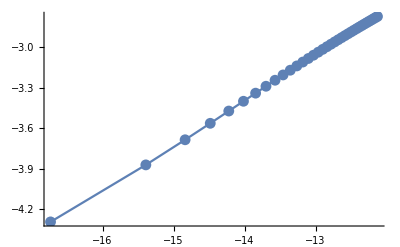

```mathematica
ListLinePlot[data=Transpose[{Table[Log[c/c0],{c,0.1,10,(10-0.1)/35}],Log[Sqrt[res*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data,{1,x},x]
```

1.30361+0.335441 x

```mathematica
fit=LinearModelFit[data,x,x]
```

FittedModel[1.30361+0.335441 x]

```mathematica
fit[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.30361 | 0.0142595 | 91.421 | 2.90703×10^-42
x | 0.335441 | 0.00108332 | 309.641 | 2.99526×10^-60, | Estimate | Standard Error | Confidence Interval
1 | 1.30361 | 0.0142595 | {1.27463,1.33259}
x | 0.335441 | 0.00108332 | {0.333239,0.337642}}

```mathematica
eqn1=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,10,100,(100-10)/35}];
```

```mathematica
res1=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn1]][[All,2]];
```

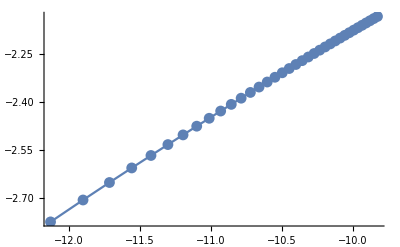

```mathematica
ListLinePlot[data1=Transpose[{Table[Log[c/c0],{c,10,100,(100-10)/35}],Log[Sqrt[res1*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data1,{1,x},x]
```

0.589013+0.276305 x

```mathematica
fit1=LinearModelFit[data1,x,x]
```

FittedModel[0.589013+0.276305 x]

```mathematica
fit1[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.589013 | 0.0109809 | 53.64 | 1.91076×10^-34
x | 0.276305 | 0.00103599 | 266.707 | 4.78144×10^-58, | Estimate | Standard Error | Confidence Interval
1 | 0.589013 | 0.0109809 | {0.566698,0.611329}
x | 0.276305 | 0.00103599 | {0.274199,0.27841}}

```mathematica
eqn2=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,100,1000,(1000-100)/35}];
```

```mathematica
res2=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn2]][[All,2]];
```

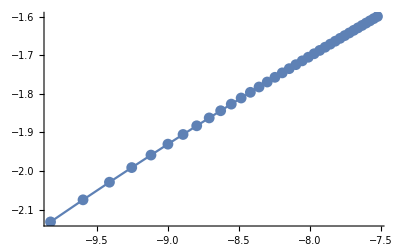

```mathematica
ListLinePlot[data2=Transpose[{Table[Log[c/c0],{c,100,1000,(1000-100)/35}],Log[Sqrt[res2*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data2,{1,x},x]
```

0.126299+0.228751 x

```mathematica
fit2=LinearModelFit[data2,x,x]
```

FittedModel[0.126299+0.228751 x]

```mathematica
fit2[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.126299 | 0.00748019 | 16.8845 | 4.21446×10^-18
x | 0.228751 | 0.000901032 | 253.877 | 2.55375×10^-57, | Estimate | Standard Error | Confidence Interval
1 | 0.126299 | 0.00748019 | {0.111098,0.141501}
x | 0.228751 | 0.000901032 | {0.22692,0.230582}}

```mathematica
eqn3=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,1000,10000,(10000-1000)/35}];
```

```mathematica
res3=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn3]][[All,2]];
```

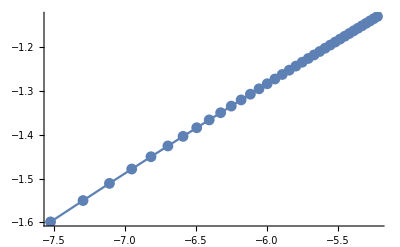

```mathematica
ListLinePlot[data3=Transpose[{Table[Log[c/c0],{c,1000,10000,(10000-1000)/35}],Log[Sqrt[res3*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data3,{1,x},x]
```

-0.069057+0.202701 x

```mathematica
fit3=LinearModelFit[data3,x,x]
```

FittedModel[-0.069057+0.202701 x]

```mathematica
fit3[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.069057 | 0.00254097 | -27.1774 | 1.20787×10^-24
x | 0.202701 | 0.000422932 | 479.276 | 1.06456×10^-66, | Estimate | Standard Error | Confidence Interval
1 | -0.069057 | 0.00254097 | {-0.0742209,-0.0638931}
x | 0.202701 | 0.000422932 | {0.201842,0.203561}}

```mathematica
eqn4=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,10000,100000,(100000-10000)/35}];
```

```mathematica
res4=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn4]][[All,2]];
```

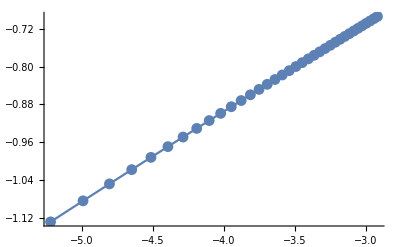

```mathematica
ListLinePlot[data4=Transpose[{Table[Log[c/c0],{c,10000,100000,(100000-10000)/35}],Log[Sqrt[res4*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data4,{1,x},x]
```

-0.141171+0.188661 x

```mathematica
fit4=LinearModelFit[data4,x,x]
```

FittedModel[-0.141171+0.188661 x]

```mathematica
fit4[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.141171 | 0.00105123 | -134.292 | 6.32346×10^-48
x | 0.188661 | 0.000282208 | 668.519 | 1.29941×10^-71, | Estimate | Standard Error | Confidence Interval
1 | -0.141171 | 0.00105123 | {-0.143307,-0.139035}
x | 0.188661 | 0.000282208 | {0.188088,0.189235}}

```mathematica
eqn5=Table[Evaluate[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,100000,1000000,(1000000-100000)/35}];
```

```mathematica
res5=Flatten[ParallelMap[FindRoot[#,{ρ,1},WorkingPrecision->40]&,eqn5]][[All,2]];
```

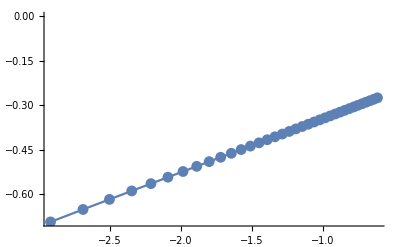

```mathematica
ListLinePlot[data5=Transpose[{Table[Log[c/c0],{c,100000,1000000,(1000000-100000)/35}],Log[Sqrt[res5*2]/fpi]}],Mesh->All]
```

```mathematica
Fit[data5,{1,x},x]
```

-0.163302+0.181402 x

```mathematica
fit5=LinearModelFit[data5,x,x]
```

FittedModel[-0.163302+0.181402 x]

```mathematica
fit5[{"ParameterTable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.163302 | 0.0000867864 | -1881.65 | 6.81936×10^-87
x | 0.181402 | 0.0000577394 | 3141.73 | 1.83817×10^-94, | Estimate | Standard Error | Confidence Interval
1 | -0.163302 | 0.0000867864 | {-0.163478,-0.163125}
x | 0.181402 | 0.0000577394 | {0.181284,0.181519}}